```mathematica
Quit[]
```

```mathematica
Start[]
```

Start[]

```mathematica
γ[s_] = {0,Cos[s],Sin[s]};
γDerivative[s_] = D[γ[s],s];
```

```mathematica
BSIntegrand[x_,y_,z_,s_] = Cross[{x,y,z}-γ[s],γDerivative[s]]/(Norm[{x,y,z}-γ[s]])^3;
BSIntegrandCircle[r_,θ_,s_] = Cross[{r Cos[θ],r Sin[θ],0}-γ[s],γDerivative[s]]/(Norm[{r Cos[θ],r Sin[θ],0}-γ[s]])^3;
```

```mathematica
BSIntegrandCircle[r,θ,s]
```

{(-Cos[s]^2-Sin[s]^2+r Cos[s] Sin[θ])/((Abs[r Cos[θ]]^2+Abs[Sin[s]]^2+Abs[-Cos[s]+r Sin[θ]]^2)^(3/2)),-(r Cos[s] Cos[θ])/((Abs[r Cos[θ]]^2+Abs[Sin[s]]^2+Abs[-Cos[s]+r Sin[θ]]^2)^(3/2)),-(r Cos[θ] Sin[s])/((Abs[r Cos[θ]]^2+Abs[Sin[s]]^2+Abs[-Cos[s]+r Sin[θ]]^2)^(3/2))}

```mathematica
BSIIntegral[x_?NumericQ,y_?NumericQ,z_?NumericQ,a_?NumericQ,b_?NumericQ] := NIntegrate[BSIntegrand[x,y,z,s],{s,a,b},AccuracyGoal-> 6];
BSIIntegralCircle[r_?NumericQ,θ_?NumericQ,a_?NumericQ,b_?NumericQ] := NIntegrate[BSIntegrandCircle[r,θ,s],{s,a,b},AccuracyGoal-> 6];
```

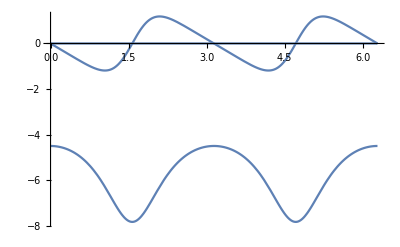

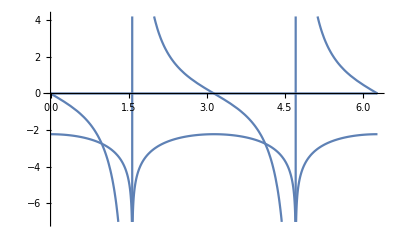

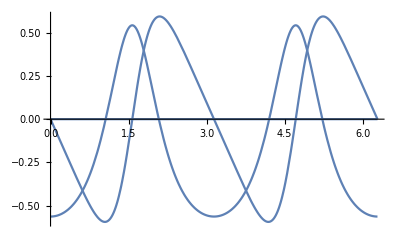

```mathematica
Plot[BSIIntegralCircle[1/2,θ,0,2π],{θ,0,2π}]
Plot[BSIIntegralCircle[1,θ,0,2π],{θ,0,2π}]
Plot[BSIIntegralCircle[2,θ,0,2π],{θ,0,2π}]
```

```mathematica
BSIIntegralCircleIntegral[r_?NumericQ,a_?NumericQ,b_?NumericQ] := NIntegrate[BSIntegrandCircle[r,θ,s],{s,a,b},{θ,0,2π},AccuracyGoal-> 6];
```

```mathematica
Chop[BSIIntegralCircleIntegral[1,0,2π]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in θ near {s,θ} = {5.30379,4.71241}. NIntegrate obtained -41.205 and 16.649 for the integral and error estimates.

{-41.205,0,0}

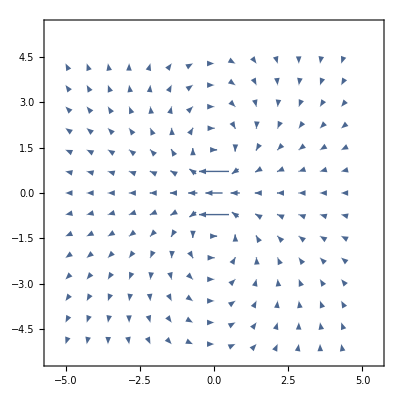

```mathematica
VectorPlot[Drop[BSIIntegral[x,y,0,0,2π],-1],{x,-5,5},{y,-5,5}]
```

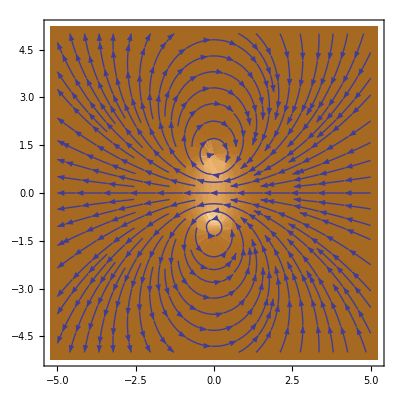

```mathematica
StreamDensityPlot[Drop[BSIIntegral[x,y,0,0,2π],-1],{x,-5,5},{y,-5,5}]
```